```mathematica
(*
Fabian Ehrentraud, 2010-07-30
Licensed under the Open Software License (OSL 3.0)
*)
```

```mathematica
Needs["PlotLegends`"]
```

```mathematica
(*Consonance Calculation Functions*)
```

```mathematica
SemiDiff[ratio_]:=Log[2,ratio]*12;
```

```mathematica
DissF[frac_]:=Numerator[frac]*Denominator[frac];
```

```mathematica
Bell[m_,s_,x_]:=ⅇ^(-(-m+x)^2/(2 s^2))
```

```mathematica
BellifyLog[fractionlist_,s_,x_]:=Function[u,1/DissF[u]*Bell[Log[2,u]*12,s,x]]/@fractionlist
```

```mathematica
Cons[fractionlist_,bellwidth_,semitonedistance_]:=Max[BellifyLog[fractionlist,bellwidth,semitonedistance]]
```

```mathematica
FragCombis[nestedlist_]:=Union[Function[u,{u,Complement[nestedlist,u]}]/@Subsets[nestedlist]/.{}->{1}]
```

```mathematica
Faxes[uptoint_]:=Flatten[Apply[Divide,Apply[Times,FragCombis/@Apply[Power,FactorInteger@Table[i,{i,1,uptoint}],{2}],{3}],{2}]]
```

```mathematica
faxes=Faxes[157];
```

```mathematica
curvex=Cons[Faxes[157],0.25,x];
```

```mathematica
just:={1,3/2,4/3,9/8,9/5,5/4,8/5,5/3,6/5,15/8,16/15,7/5,2}
```

```mathematica
just2=Union[just/2,just];
```

```mathematica
justbell=BellifyLog[just2,0.25,x];
```

```mathematica
(*Unused Stuff*)
```

```mathematica
NoteOctave[ratio_]:=Floor[Log[2,ratio]];
```

```mathematica
NoteNumR[ratio_]:=Round[Log[2,ratio]*12];
```

```mathematica
notenames:={"C","C#","D","D#","E","F","F#","G","G#","A","A#","H"};notenames::usage="notes in an equal temperament octave";
```

```mathematica
Notename[notenum_]:=notenames[[Mod[notenum,Length[notenames]]+1]];Notename::usage="gives the notename (from notenames) to a midi note number";
```

```mathematica
NotenameR[ratio_]:=notenames[[Mod[Round[(Log[2,ratio])*12],Length[notenames]]+1]]<>ToString[NoteOctave[ratio]];NotenameR::usage="gives back the notename (from notenames) for a ratio";
```

```mathematica
middleA:=440;middleA::usage="the frequency of middle a in Hz";
middleANotenum:=69;middleANotenum::usage="the midi note number of middle a";
```

```mathematica
NoteNum[freq_]:=Round[(Log[2,freq]-Log[2,middleA])*12]+middleANotenum ;NoteNum::usage="calculates the midi note number of a frequency";
```

```mathematica
CentOff[freq_]:=(Log[2,freq]-Log[2,middleA])*1200-100*Round[(Log[2,freq]-Log[2,middleA])*12] ;CentOff::usage="calculates the cent offset of a given frequency to the nearest midi note, in range of [-50,50]";
```

```mathematica
SortByDiss[ratiolist_]:=Sort[ratiolist,DissF[#1]<DissF[#2]&]
```

```mathematica
SortByCent[ratiolist_]:=Sort[ratiolist,Log[2,#1]<Log[2,#2]&]
```

```mathematica
SelectLowestDistForNote[sortedratiolist_,notenum_]:=Select[sortedratiolist,NoteNumR@#==notenum&,1];(*list must already be sorted by diss*)
```

```mathematica
SelectLowestDist[sortedratiolist_]:=Flatten[Table[SelectLowestDistForNote[sortedratiolist,notenum],{notenum,Union[NoteNumR@sortedratiolist]}]];(*for all note numbers respectively*)
```

```mathematica
(*Diagrams*)
```

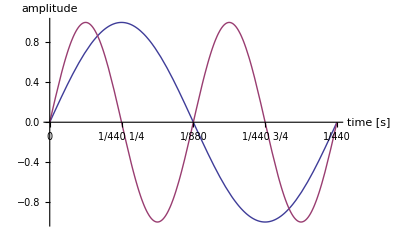

```mathematica
Plot[{Sin[440*2*Pi*x],Sin[2*440*2*Pi*x]},{x,0,1/440},AxesLabel->{"time [s]","amplitude"},Ticks->{{0,{2/8*1/440,Format[2/8]*Format[1/440]},{4/8*1/440,Format[1/2*1/440]},{6/8*1/440,Format[6/8]*Format[1/440]},{8/8*1/440,Format[1/440]}},Automatic},PlotStyle->Thick,PlotLegend->{"440Hz","880Hz"},LegendPosition->{1.1,-0.4},LegendShadow->None,Background->White]
```

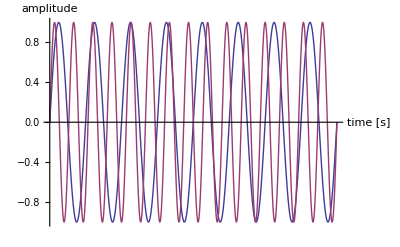

```mathematica
Plot[{Sin[440*2*Pi*x],Sin[15/8*440*2*Pi*x]},{x,0,8/440},AxesLabel->{"time [s]","amplitude"},Ticks->{(*{0,{2/8*1/440,Format[2/8]*Format[1/440]},{4/8*1/440,Format[1/2*1/440]},{6/8*1/440,Format[6/8]*Format[1/440]},{8/8*1/440,Format[1/440]}}*)None,Automatic},PlotStyle->Thick,PlotLegend->{"440Hz","825Hz"},LegendPosition->{1.1,-0.4},LegendShadow->None,Background->White]
```

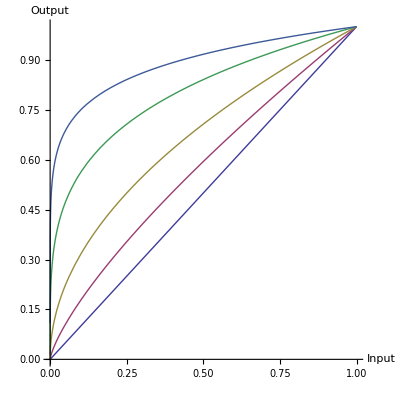

```mathematica
Plot[{x,x^0.75,x^0.5,x^0.25,x^0.125(*,Log[2,x]/8+1*)},{x,0,1},AxesLabel->{"Input","Output"},AspectRatio->1,PlotLegend->{1,0.75,0.5,0.25,0.125},LegendPosition->{1.1,-0.4},LegendShadow->None,Background->White]
```

```mathematica
1/256//N
```

0.00390625

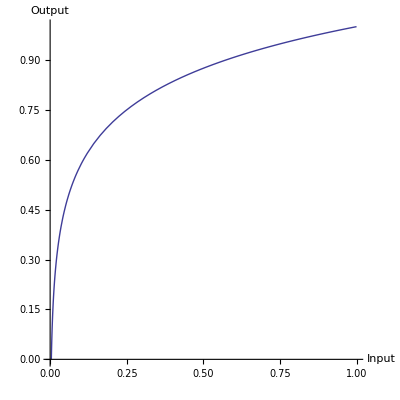

```mathematica
Plot[(Log[x]/Log[2])/8+1,{x,0,1},PlotRange->{0,1},AxesLabel->{"Input","Output"},AspectRatio->1(*,PlotLegend->{1,0.75,0.5,0.25,0.125},LegendPosition->{1.1,-0.4},LegendShadow->None*),Background->White]
```

```mathematica
Manipulate[Plot[Piecewise[{{x/a,x<a},{1-(x-a)*(1-s)/d,x<a+d},{s,x<a+d+sr},{s-(x-a-d-sr)*s/r,x<a+d+sr+r}}],{x,0,a+d+sr+r},PlotRange->{0,1},Background->White],{{a,10},0,20},{{d,20},0,50},{{sr,30},0,100},{{s,0.8},0,1},{{r,50},0,100}]
```

```mathematica
(*unfortunately, i could not export the picture generated with the Manipulate command without the controls*)
```

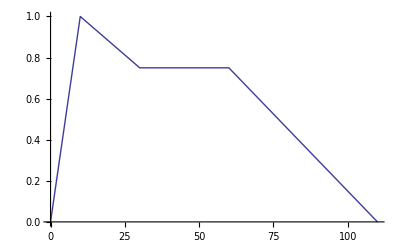

```mathematica
Plot[Piecewise[{{x/a,x<a},{1-(x-a)*(1-s)/d,x<a+d},{s,x<a+d+sr},{s-(x-a-d-sr)*s/r,x<a+d+sr+r}}],{x,0,a+d+sr+r},PlotRange->{0,1},Background->White]/.{a->10,d->20,s->0.75,sr->30,r->50}
```

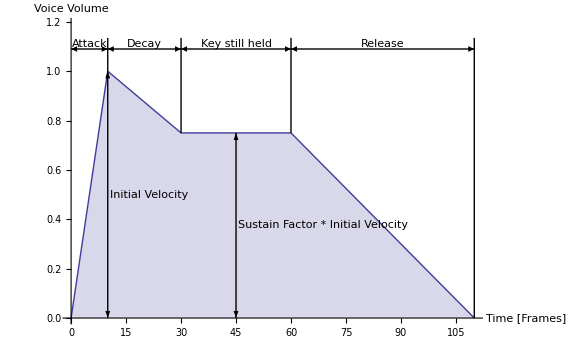

```mathematica
Plot[Piecewise[{{x/a,x<a},{1-(x-a)*(1-s)/d,x<a+d},{s,x<a+d+sr},{s-(x-a-d-sr)*s/r,x<a+d+sr+r}}],{x,0,a+d+sr+r},PlotRange->{0,1+h+0.1},AxesLabel->{"Time [Frames]","Voice Volume"},Filling->Axis,PlotStyle->Thick,Epilog->{Arrowheads[{-0.025,0.025}],Arrow[{{0,1+h},{a,1+h}}],Arrow[{{a,1+h},{a+d,1+h}}],Arrow[{{a+d,1+h},{a+d+sr,1+h}}],Arrow[{{a+d+sr,1+h},{a+d+sr+r,1+h}}],Arrow[{{a,0},{a,1}}],Arrow[{{a+d+sr/2,0},{a+d+sr/2,s}}],Text["Attack",{a/2,1+h},{Center,Bottom}],Text["Decay",{a+d/2,1+h},{Center,Bottom}],Text["Key still held",{a+d+sr/2,1+h},{Center,Bottom}],Text["Release",{a+d+sr+r/2,1+h},{Center,Bottom}],Text["Initial Velocity",{a+0.5,1/2},{Left,Center}],Text["Sustain Factor * Initial Velocity",{a+d+sr/2+0.5,s/2},{Left,Center}],Line[{{a,1},{a,1+h+h/2}}],Line[{{a+d,s},{a+d,1+h+h/2}}],Line[{{a+d+sr,s},{a+d+sr,1+h+h/2}}],Line[{{a+d+sr+r,0},{a+d+sr+r,1+h+h/2}}]},Background->White]/.{a->10,d->20,s->0.75,sr->30,r->50,h->0.09}
```

```mathematica
Manipulate[Plot[Piecewise[{{x/a,x<a},{1-(x-a)/r,x<a+r}}],{x,0,a+r},PlotRange->{0,1},Background->White],{{a,10},0,20},{{r,50},0,100}]
```

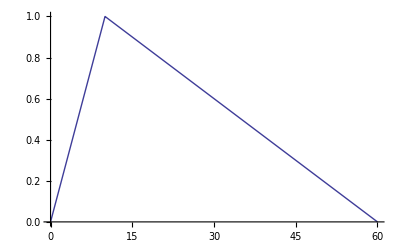

```mathematica
Plot[Piecewise[{{x/a,x<a},{1-(x-a)/r,x<a+r}}],{x,0,a+r},PlotRange->{0,1},Background->White]/.{a->10,r->50}
```

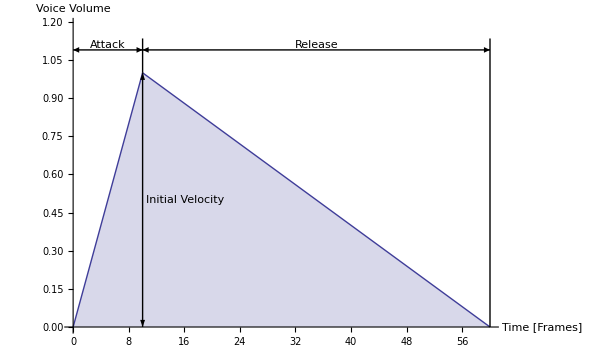

```mathematica
Plot[Piecewise[{{x/a,x<a},{1-(x-a)/r,x<a+r}}],{x,0,a+r},PlotRange->{0,1+h+0.1},AxesLabel->{"Time [Frames]","Voice Volume"},Filling->Axis,PlotStyle->Thick,Epilog->{Arrowheads[{-0.025,0.025}],Arrow[{{0,1+h},{a,1+h}}],Arrow[{{a,1+h},{a+r,1+h}}],Arrow[{{a,0},{a,1}}],Text["Attack",{a/2,1+h},{Center,Bottom}],Text["Release",{a+r/2,1+h},{Center,Bottom}],Text["Initial Velocity",{a+0.5,1/2},{Left,Center}],Line[{{a,1},{a,1+h+h/2}}],Line[{{a+r,0},{a+r,1+h+h/2}}]},Background->White]/.{a->10,r->50,h->0.09}
```

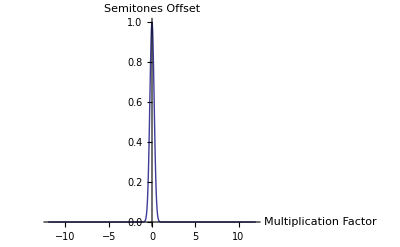

```mathematica
Plot[E^-(((-12*Log[2,1]+x)^2)/(2*0.25^2)),{x,-12,12},AxesLabel->{"Multiplication Factor","Semitones Offset"},PlotRange->Full,PlotLegend->{"bellWidth = 0.25"},LegendPosition->{0.1,-0.1},LegendShadow->None,PlotStyle->Thick,Background->White]
```

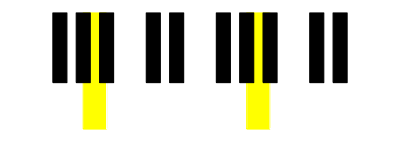

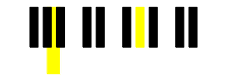

```mathematica
Graphics[{Table[{EdgeForm[Thick],If[MemberQ[{2,9},x],Yellow,White],Rectangle[{x,0},{x+1,-5},RoundingRadius->0.1]},{x,0,13}],Table[{EdgeForm[Thick],If[MemberQ[{},x],Yellow,Black],Rectangle[{x+1-0.3,0},{x+1.3,-3},RoundingRadius->0.1]},{x,Select[Range[0,13-1],Mod[#+3,7]≠2&&Mod[#+3,7]≠6&]}]},Background->White]
```

```mathematica
440*15/8
```

825

```mathematica
440*2^(11/12)//N
```

830.609

```mathematica
Log[2,1732/1731]*12//N
```

0.00999846

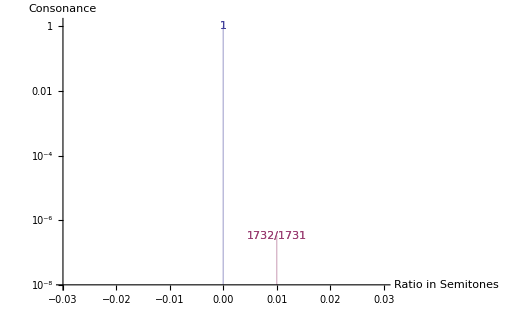

```mathematica
ListLogPlot[Function[u,{{SemiDiff[u],1/DissF[u]}}]/@{1,1732/1731},Filling->Axis,PlotRange->{{-0.03,0.03},{0.00000001,1.2}},PlotMarkers->{{1/1},{1732/1731}},AxesLabel->{"Ratio in Semitones","Consonance"},Background->White]
```

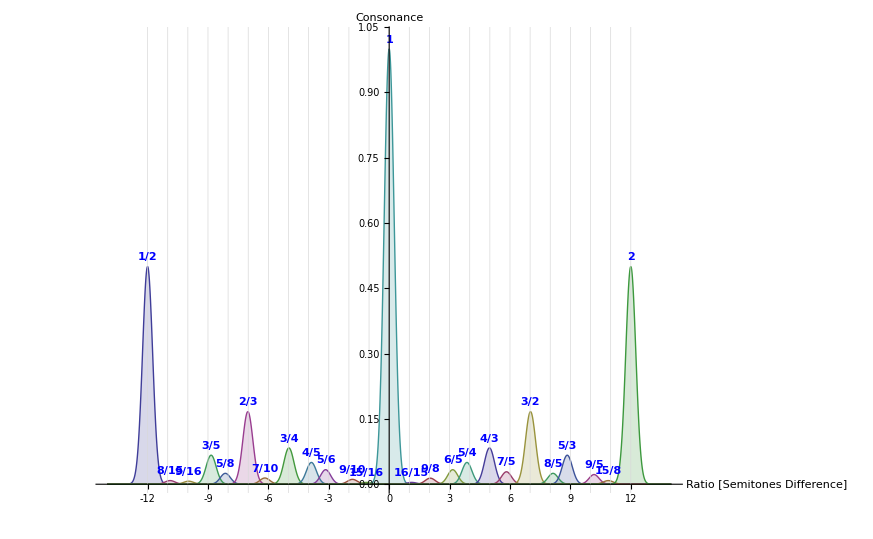

```mathematica
Plot[(*BellifyLog[nature2,0.35,x]*)justbell,{x,-14,14},Filling->Axis,PlotRange->{{-14,14},{0(*.001*),1.03}}(*,Mesh->Full(**)*),GridLines->{Table[i,{i,-12,12}],(*)Table[Max[BellifyLog[just2,0.35,x]],{x,-12,12}]( *)None(**)},Ticks->{Table[i,{i,-12,12}],Automatic},Epilog->{Function[u,Text[Style[u,Bold,Blue],{SemiDiff[u]+0,1/DissF[u]+0.01},{Center,Bottom},Background->White]]/@just2},AxesLabel->{"Ratio [Semitones Difference]","Consonance"},Background->White]
```

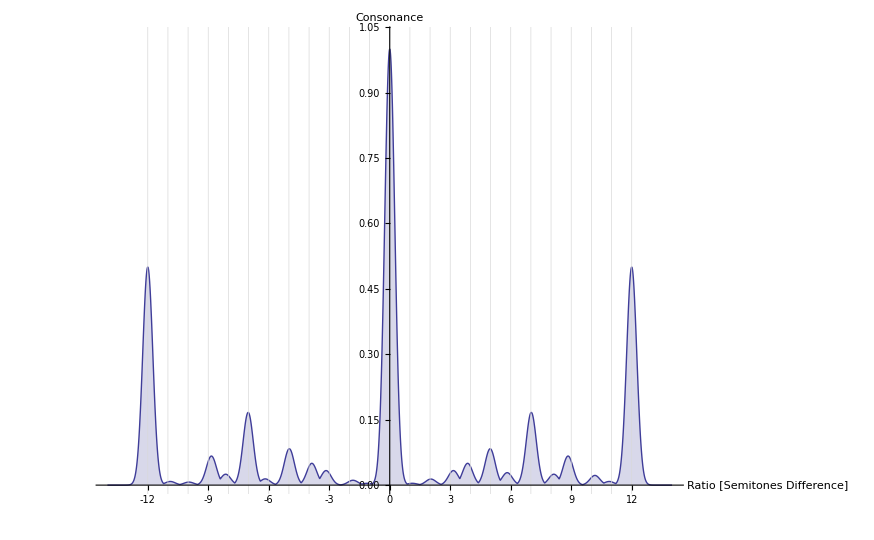

```mathematica
Plot[Max[justbell],{x,-14,14},Filling->Axis,PlotRange->{{-14,14},{0(*.001*),1.03}}(*,Mesh->Full(**)*),GridLines->{Table[i,{i,-12,12}],(*)Table[Max[BellifyLog[just2,0.35,x]],{x,-12,12}]( *)None(**)},Ticks->{Table[i,{i,-12,12}],Automatic},(*Epilog->{Function[u,Text[Style[u,Bold,Blue],{SemiDiff[u]+0,1/DissF[u]+0.01},{Center,Bottom},Background->White]]/@just2},*)AxesLabel->{"Ratio [Semitones Difference]","Consonance"},Background->White]
```

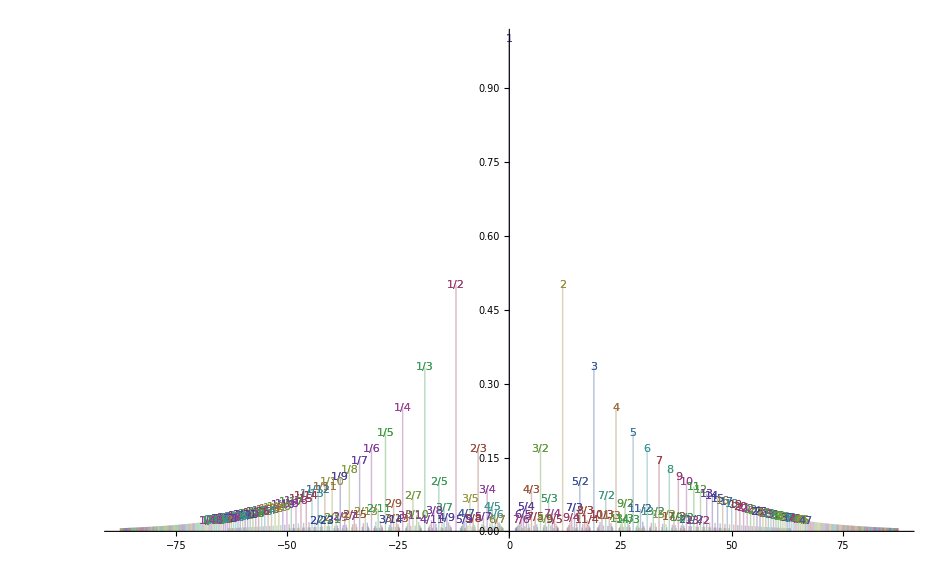

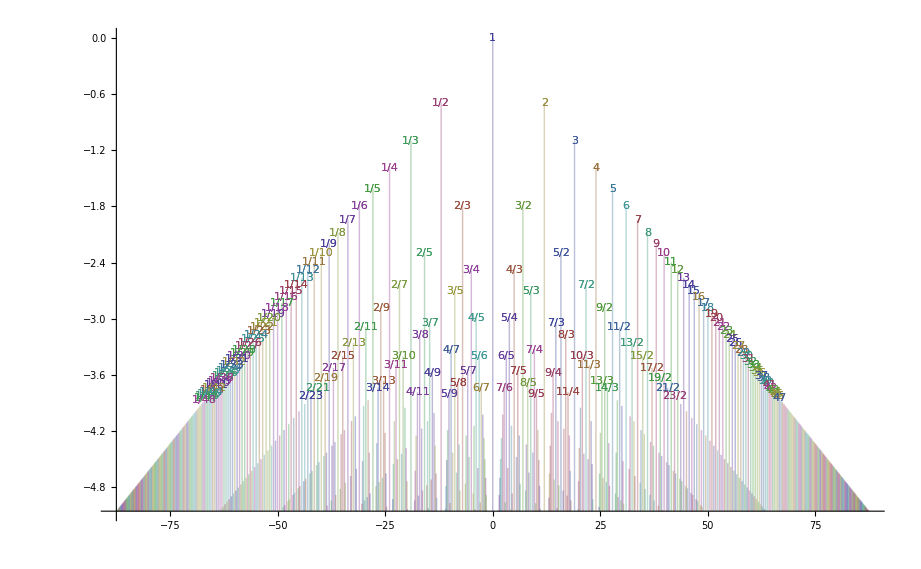

```mathematica
ListPlot[Function[u,{{SemiDiff[u],1/DissF[u]}}]/@faxes,Filling->Axis,PlotRange->Full,PlotMarkers->faxes,AxesLabel->{"Ratio [Semitones Difference]","Consonance"},Background->White]
```

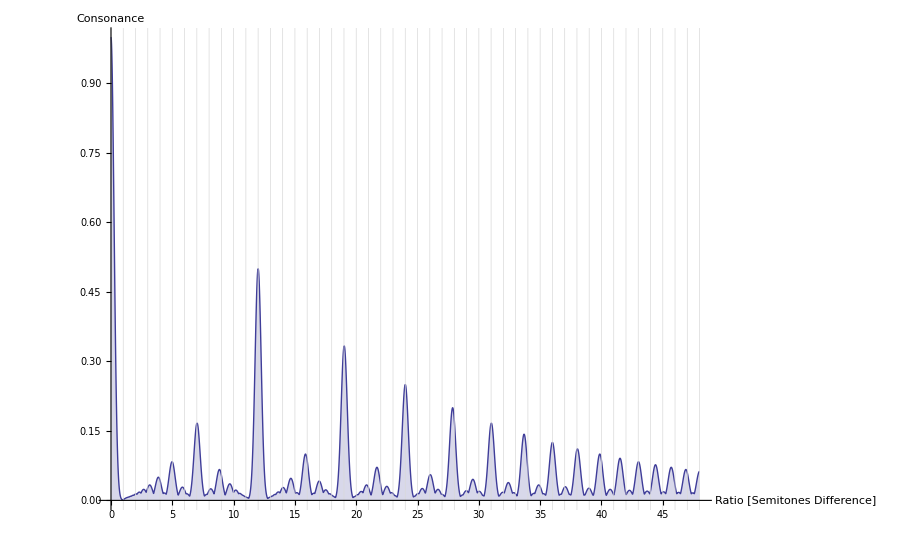

```mathematica
Plot[curvex^(1),{x,0,4*12},Filling->Axis,PlotRange->{{0,4*12},{0,1}}(*,Mesh->Full(**)*),GridLines->{Table[i,{i,0,4*12}],(*Table[curvex^(1),{x,0,4*12}]*)None},Ticks->{Table[i,{i,0,4*12}],Automatic},AxesLabel->{"Ratio [Semitones Difference]","Consonance"},Background->White]
```

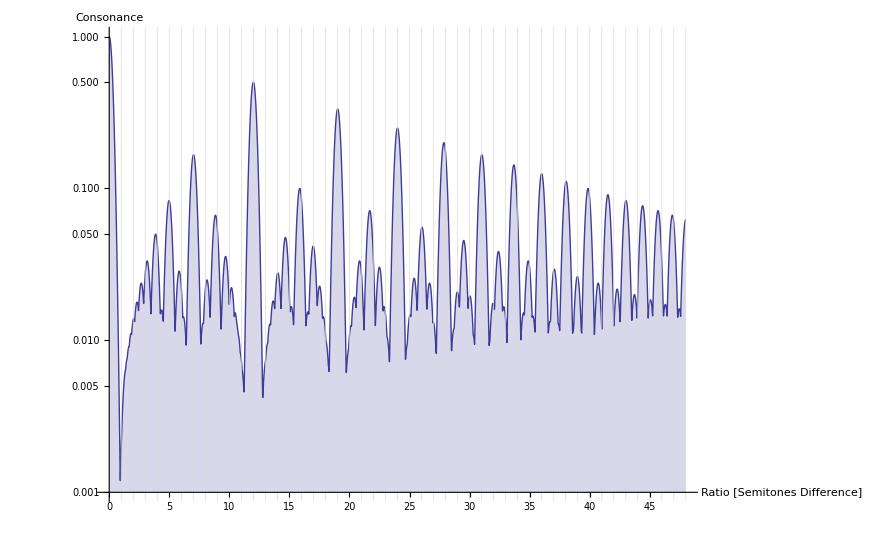

```mathematica
LogPlot[curvex^(1),{x,0,4*12},Filling->Axis,PlotRange->{{0,4*12},{0.001,1}}(*,Mesh->Full(**)*),GridLines->{Table[i,{i,0,4*12}],(*Table[curvex^(1),{x,0,4*12}]*)None},Ticks->{Table[i,{i,0,4*12}],Automatic},AxesLabel->{"Ratio [Semitones Difference]","Consonance"},Background->White]
```